PRACTICAL 7

To perform the Taylor’s series expansion of a given function f(z) around a given point z

Ques1. f [z] = Exp [z] , z = 0 , n = 6

The given function f(z)=ⅇ^z

The Taylor series Expansion of f(z) around z=0is 
1+z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/720

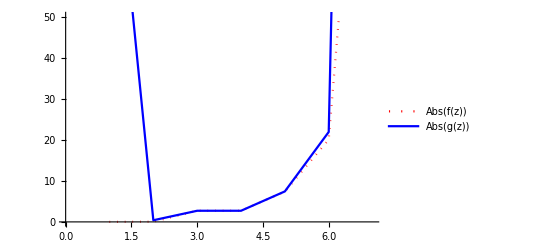

```mathematica
f[z_]=Exp[z];
z0=0;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,6}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red,Dotted}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

Ques2 . f[z] = 1 / (4 - z^2) , z = 0 , n = 30

The given function f(z)=1/(4-z^2)

The Taylor series Expansion of f(z) around z=0is 
1/4+z^2/16+z^4/64+z^6/256+z^8/1024+z^10/4096+z^12/16384+z^14/65536+z^16/262144+z^18/1048576+z^20/4194304+z^22/16777216+z^24/67108864+z^26/268435456+z^28/1073741824+z^30/4294967296

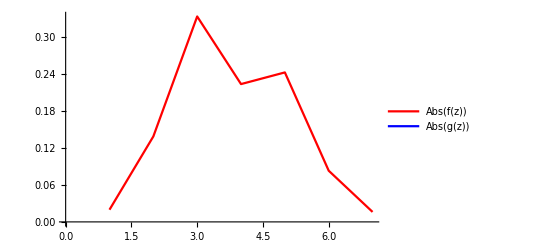

```mathematica
f[z_]=1/(4-z^2);
z0=0;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,30}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

Ques 3.  f[z] = z / (z^4 + 9) , z = 0 , n = 10

The given function f(z)=z/(9+z^4)

The Taylor series Expansion of f(z) around z=0is 
z/9-z^5/81+z^9/729

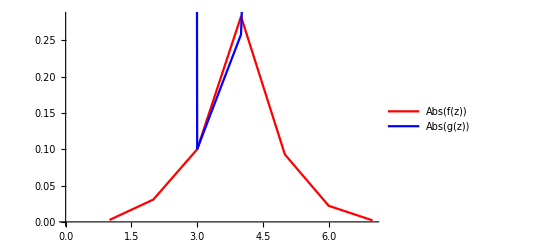

```mathematica
f[z_]=z/(z^4+9);
z0=0;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,10}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

Ques 4.  f[z] = (1+2 z^2) / (z^3 + z^5) , z =0 , n = 10

The given function f(z)=(1+2 z^2)/(z^3+z^5)

The Taylor series Expansion of f(z) around z=0is 
1/z^3+1/z-z+z^3-z^5+z^7-z^9

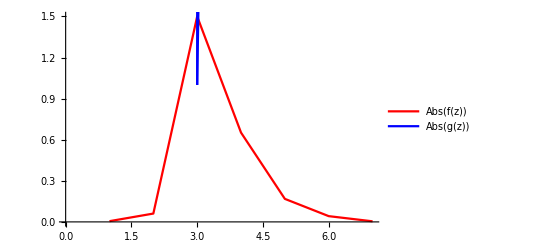

```mathematica
f[z_]=(1+2  z^2)/(z^3+z^5);
z0=0;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,10}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

Ques  5. f [z] = 1 / (1 - z) , z = 2 , n = 30

The given function f(z)=1/(1-z)

The Taylor series Expansion of f(z) around z=2is 
-3-(-2+z)^2+(-2+z)^3-(-2+z)^4+(-2+z)^5-(-2+z)^6+(-2+z)^7-(-2+z)^8+(-2+z)^9-(-2+z)^10+(-2+z)^11-(-2+z)^12+(-2+z)^13-(-2+z)^14+(-2+z)^15-(-2+z)^16+(-2+z)^17-(-2+z)^18+(-2+z)^19-(-2+z)^20+(-2+z)^21-(-2+z)^22+(-2+z)^23-(-2+z)^24+(-2+z)^25-(-2+z)^26+(-2+z)^27-(-2+z)^28+(-2+z)^29-(-2+z)^30+z

Power::infy: Infinite expression 1/0 encountered.

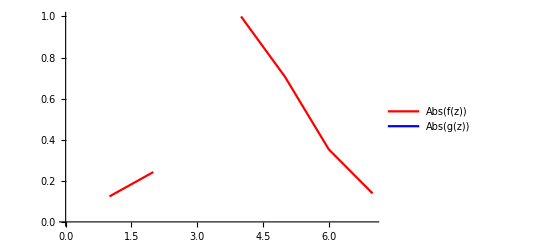

```mathematica
f[z_]=1/(1-z);
z0=2;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,30}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

Ques 6. f [z] = cos [z] , z = 1 , n = 15

The given function f(z)=Cos[z]

The Taylor series Expansion of f(z) around z=1is 
Cos[1]-1/2 (-1+z)^2 Cos[1]+1/24 (-1+z)^4 Cos[1]-1/720 (-1+z)^6 Cos[1]+((-1+z)^8 Cos[1])/40320-((-1+z)^10 Cos[1])/3628800+((-1+z)^12 Cos[1])/479001600-((-1+z)^14 Cos[1])/87178291200-(-1+z) Sin[1]+1/6 (-1+z)^3 Sin[1]-1/120 (-1+z)^5 Sin[1]+((-1+z)^7 Sin[1])/5040-((-1+z)^9 Sin[1])/362880+((-1+z)^11 Sin[1])/39916800-((-1+z)^13 Sin[1])/6227020800+((-1+z)^15 Sin[1])/1307674368000

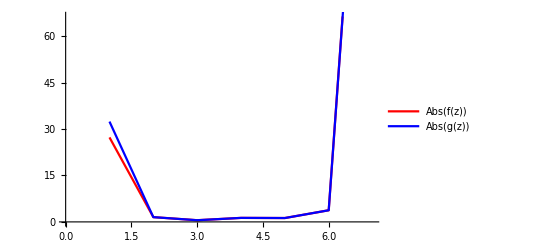

```mathematica
f[z_]=Cos[z];
z0=1;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,15}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

Ques7. f [z] = sin[z] , z = 1 , n = 20

The given function f(z)=Sin[z]

The Taylor series Expansion of f(z) around z=1is 
(-1+z) Cos[1]-1/6 (-1+z)^3 Cos[1]+1/120 (-1+z)^5 Cos[1]-((-1+z)^7 Cos[1])/5040+((-1+z)^9 Cos[1])/362880-((-1+z)^11 Cos[1])/39916800+((-1+z)^13 Cos[1])/6227020800-((-1+z)^15 Cos[1])/1307674368000+((-1+z)^17 Cos[1])/355687428096000-((-1+z)^19 Cos[1])/121645100408832000+Sin[1]-1/2 (-1+z)^2 Sin[1]+1/24 (-1+z)^4 Sin[1]-1/720 (-1+z)^6 Sin[1]+((-1+z)^8 Sin[1])/40320-((-1+z)^10 Sin[1])/3628800+((-1+z)^12 Sin[1])/479001600-((-1+z)^14 Sin[1])/87178291200+((-1+z)^16 Sin[1])/20922789888000-((-1+z)^18 Sin[1])/6402373705728000+((-1+z)^20 Sin[1])/2432902008176640000

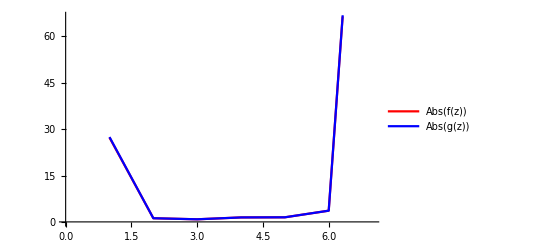

```mathematica
f[z_]=Sin[z];
z0=1;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,20}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

Ques 8. f [z] = sin[z^2] , z = 1 , n = 15

The given function f(z)=Sin[z^2]

The Taylor series Expansion of f(z) around z=0is 
z^2-z^6/6+z^10/120-z^14/5040

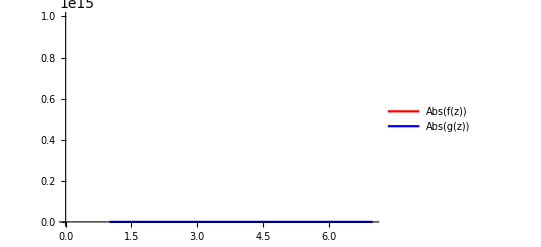

```mathematica
f[z_]=Sin[z^2];
z0=0;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,15}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

```mathematica
Ques 9. f[z]=Exp[z^2],z=1,n=7
```

The given function f(z)=ⅇ^(z^2)

The Taylor series Expansion of f(z) around z=1is 
ⅇ+2 ⅇ (-1+z)+3 ⅇ (-1+z)^2+10/3 ⅇ (-1+z)^3+19/6 ⅇ (-1+z)^4+13/5 ⅇ (-1+z)^5+173/90 ⅇ (-1+z)^6+407/315 ⅇ (-1+z)^7

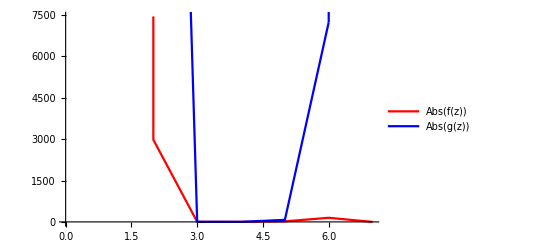

```mathematica
f[z_]=Exp[z^2];
z0=1;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,7}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

```mathematica
Ques 10.f[z]=Sinh[z],z=0,n=4
```

The given function f(z)=Sinh[z]

The Taylor series Expansion of f(z) around z=0is 
z+z^3/6

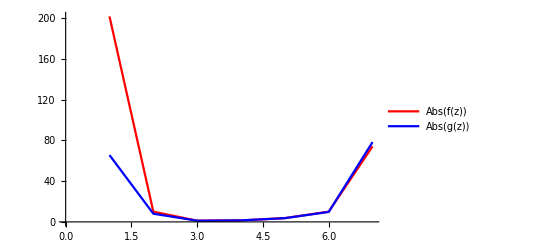

```mathematica
f[z_]=Sinh[z];
z0=0;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,4}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```

```mathematica
Ques 11. f[z]=tan[z],z=1,n=4
```

The given function f(z)=Tan[z]

The Taylor series Expansion of f(z) around z=1is 
Tan[1]+(-1+z) (1+Tan[1]^2)+(-1+z)^2 (Tan[1]+Tan[1]^3)+1/3 (-1+z)^3 (1+4 Tan[1]^2+3 Tan[1]^4)+1/3 (-1+z)^4 (2 Tan[1]+5 Tan[1]^3+3 Tan[1]^5)

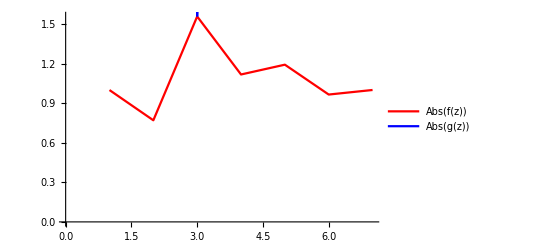

```mathematica
f[z_]=Tan[z];
z0=1;
Z={-6+4I,-3-I,1,1+I,2+I,3+2I,5+6I};
g[z_]=Normal[Series[f[z],{z,z0,4}]];
Print["The given function f(z)=",f[z]];
Print["The Taylor series Expansion of f(z) around z=",z0,"is \n",g[z]]
k=ListLinePlot[Table[Abs[f[z]],{z,Z}],PlotLegends->{"Abs(f(z))"},PlotStyle->{Red}];
h=ListLinePlot[Table[Abs[g[z]],{z,Z}],PlotLegends->{"Abs(g(z))"},PlotStyle->{Blue}];
Show[k,h]
```